```mathematica
Dynamic[p1]
Dynamic[p2]
iteration=0;

makeData[arg_]:=SortBy[ToExpression[{(arg/.data)[[All,1]],(arg/.data)[[All,2]]}ᵀ],#[[1]]&];
numSteps=100;
While[iteration<numSteps+1,
yam=Import["/Users/samuelbarber/Library/CloudStorage/GoogleDrive-sbarber@lbl.gov/My Drive/sandbox/python/xopt/dump.yaml","YAML"];

data="data"/.yam;
dataKeys=data[[All,1]];
controlKeys=Select[dataKeys,#!="f"&&#!="xopt_error"&&#!="xopt_runtime"&];
list={};

For[i=1,i<Length[controlKeys]+1,i++,
list=Append[list,makeData[controlKeys[[i]]]]
];

p2=ListLinePlot[list,PlotLegends->controlKeys,PlotRange-> {{0,numSteps},{0,1}},Frame-> True];
p1=ListLinePlot[makeData["f"],PlotRange-> {{0,numSteps},{0,1}},Frame-> True];

(*p1=ListLinePlot[Select[list,#[[1]]=="f"&][[1,2]],PlotRange-> {{0,40},{0,1}},Frame-> True];

p2=ListLinePlot[{Select[list,#[[1]]=="JetX"&][[1,2]],Select[list,#[[1]]=="JetY"&][[1,2]],Select[list,#[[1]]=="JetZ"&][[1,2]],Select[list,#[[1]]=="GratingSeparation"&][[1,2]]},PlotRange-> {{0,40},{0,1}},Frame-> True];*)

iteration=Length[list[[1]]];
Pause[1]
]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

```mathematica
list[[1]]
```

{{1,0.1},{10,0.505083},{11,0.437817},{12,0.453428},{13,0.523774},{14,0.522967},{15,0.503663},{16,0.505833},{17,0.506254},{18,0.505973},{19,0.504981},{2,0.5},{20,0.505249},{21,0.502225},{22,0.499865},{23,0.475299},{24,0.540291},{25,0.505011},{26,0.504961},{27,0.50543},{28,0.504954},{29,0.504867},{3,0.500905},{30,0.504815},{31,0.504963},{32,0.504936},{33,0.504852},{34,0.504844},{35,0.504683},{36,0.506476},{37,0.504771},{38,0.505854},{39,0.506342},{4,0.491523},{40,0.50662},{41,0.506211},{42,0.506656},{5,0.543397},{6,0.504056},{7,0.505058},{8,0.502092},{9,0.501521}}

```mathematica
makeData[dataKeys[[1]]]
```

{{1,0.1},{10,0.505083},{11,0.437817},{12,0.453428},{13,0.523774},{14,0.522967},{15,0.503663},{16,0.505833},{17,0.506254},{18,0.505973},{19,0.504981},{2,0.5},{20,0.505249},{21,0.502225},{22,0.499865},{23,0.475299},{24,0.540291},{25,0.505011},{26,0.504961},{27,0.50543},{28,0.504954},{29,0.504867},{3,0.500905},{30,0.504815},{31,0.504963},{32,0.504936},{33,0.504852},{34,0.504844},{35,0.504683},{36,0.506476},{37,0.504771},{38,0.505854},{39,0.506342},{4,0.491523},{40,0.50662},{41,0.506211},{42,0.506656},{5,0.543397},{6,0.504056},{7,0.505058},{8,0.502092},{9,0.501521}}

```mathematica
SortBy[{("JetX"/.data)[[All,1]],("JetX"/.data)[[All,2]]}ᵀ,#[[1]]&]
```

{{1,0.1},{10,0.904329},{11,0.877704},{12,0.859344},{13,0.912965},{14,0.913882},{15,0.901375},{16,0.903425},{17,0.902558},{18,0.902928},{19,0.903679},{2,0.9},{20,0.903449},{21,0.905334},{22,0.906809},{23,0.920651},{24,0.889258},{25,0.883861},{26,0.881408},{27,0.858808},{28,0.884927},{29,0.884743},{3,0.901809},{30,0.883289},{31,0.88773},{32,0.891135},{33,0.891056},{34,0.890865},{35,0.885362},{36,0.926835},{37,0.889093},{38,0.911313},{39,0.916288},{4,0.883048},{40,0.916913},{41,0.926843},{42,0.944302},{5,0.986776},{6,0.908111},{7,0.910123},{8,0.903977},{9,0.903588}}

37

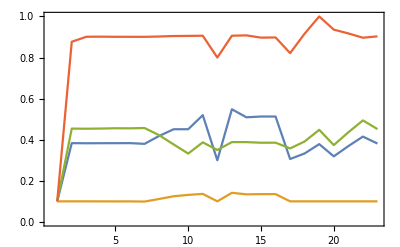

```mathematica
Length[Select[list,#[[1]]=="f"&][[1,2]]]
```